```mathematica
NN = 6
m0[a_] := ⅇ^(1/NN Log[a])

σ0[a_] := ⅇ^(1/NN Log[ 1 + a])



mj[a_,j_] := m0[a] ⅇ^(2 π ⅈ j / NN)

m1[a_] := m0[a] ⅇ^(2 π ⅈ  / NN)

σ1[a_] := σ0[a]  ⅇ^((2 π ⅈ)/NN)



W0[a_] := (- 1)/(2π)( NN σ0[a] + ∑_(j=0)^(NN-1) mj[a,j] Log[ σ0[a] - mj[a,j] ])



W1[a_] := -1/(2π) (NN σ1[a] + ∑_(j=0)^(NN-1) mj[a,j] Log[ σ1[a] - mj[a,j] ] )



Tower[a_, k_] := (( ⅇ^(2 π ⅈ / NN) - 1 ) W0[a] + ⅈ mj[a,k])/(m1[a] - m0[a])

rmax = ⅇ^2
logz[x_,y_] := ⅇ^(ⅈ Arg[ x + ⅈ y]) (x^2 + y^2)^(NN/2)
```

6

ⅇ^2

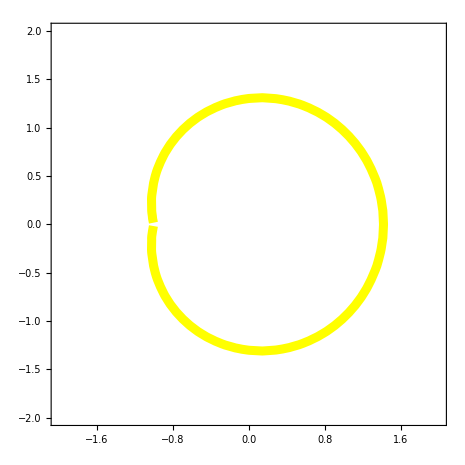

```mathematica
ContourPlot[   {  Re[ Tower[x + ⅈ y, 1] ] == 0  },
                             { x , -2, 2}, { y, -2, 2 },
                             ContourStyle->{ Directive[ Thickness[0.014], Yellow ] }   ]
```

```mathematica
FindRoot[ Re[ Tower[x, 2] ], {x, 10.} ]
```

{x→295.022}

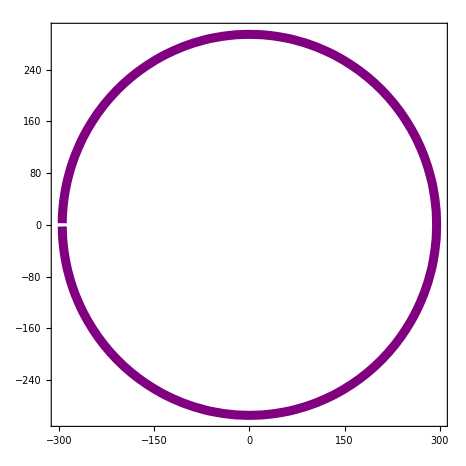

```mathematica
ContourPlot[   {  Re[ Tower[x + ⅈ y, 2] ] == 0  },
                             { x , -300, 300 },{y, -300, 300},
                             ContourStyle->{ Directive[ Thickness[0.014], Purple ] }   ]
```

```mathematica
FindRoot[ Re[ Tower[x, 3] ], {x, 10.} ]
```

{x→68042.4}

```mathematica
L = 70000
```

70000

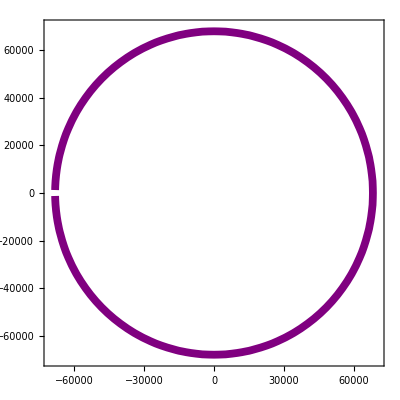

```mathematica
ContourPlot[   {  Re[ Tower[x + ⅈ y, 3] ] == 0  },
                             {x, -L, L},{y, -L, L},
                             ContourStyle->{ Directive[ Thickness[0.014], Purple ] }   ]
```

```mathematica
FindRoot[ Re[ Tower[x, 4] ], {x, 10.} ]
```

{x→68042.4}

```mathematica
L = 70000;
ContourPlot[   {  Re[ Tower[x + ⅈ y, 4] ] == 0  },
                             {x, -L, L},{y, -L, L},
                             ContourStyle->{ Directive[ Thickness[0.014], Purple ] }   ]
```

-Graphics-

```mathematica
FindRoot[ Re[ Tower[x, 5] ], {x, 10.} ]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{x→295.022}

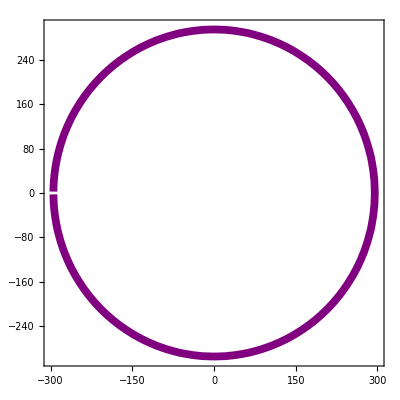

```mathematica
L = 300;
ContourPlot[   {  Re[ Tower[x + ⅈ y, 5] ] == 0  },
                             {x, -L, L},{y, -L, L},
                             ContourStyle->{ Directive[ Thickness[0.014], Purple ] }   ]
```

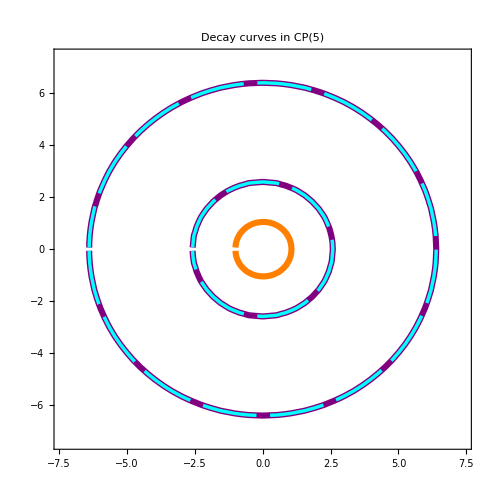

```mathematica
ContourPlot[    Evaluate[   Table[ Re[ Tower[ logz[x, y], j] ] == 0 , { j, NN -1} ]   ], 
                             { x , -rmax, rmax}, { y, -rmax, rmax },
                             ContourStyle->
                          Join[ { Directive[ Thickness[0.009], Orange ]  },
                       Table[ Directive[ Thickness[0.009], Purple ], {k,Ceiling[NN/2] -1 }] ,
                       Table[ Directive[ Thickness[0.005],Cyan, Dashing->{0.08,0.02} ], {k,NN -1 - Ceiling[NN/2] }] ] ,
                            PlotLabel-> Style["Decay curves in CP(5)",FontSize->24], LabelStyle->Directive[FontSize->18]]
```

```mathematica
R = x /.FindRoot[ Re[ Tower[x, Ceiling[NN/2]] ], {x, 10.} ]
R^(1/NN)
```

68042.4

6.38945